```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,50];
```

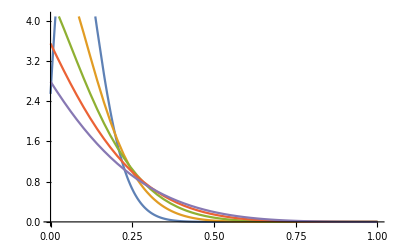

```mathematica
Plot[Evaluate[Table[neutral/. {x->0.1, t->time},{time, {0.05,0.1,0.15,0.2,0.25}}]], {y,0,1}]
```

```mathematica
Quit[]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_30Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward30[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
α = 0.01
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
VG = 0.00101;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
```

0.01

```mathematica
expectation = 0.1;
print[expectation]
```

print[0.1]

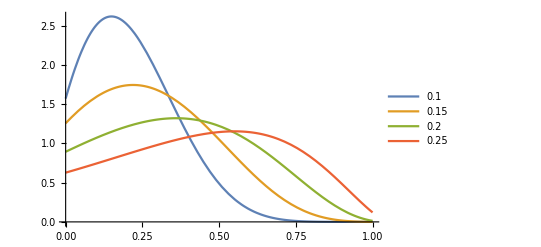

```mathematica
Plot[Evaluate[Table[SimplifiedHayward30[5]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{time,{0.1,0.15,0.2,0.25}}]],{y,0,1},PlotLegends->{0.1,0.15,0.2,0.25}]
```